# ARTIQ DATA PROCESSING

## Last Updated: 2025/09/05

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## Phonon Conversion

### Coherent_C

```mathematica
(*coherent_c: convert R/B ratio to <n> assuming a coherent state*)
```

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

### Coherent_R

```mathematica
(*coherent_c: convert RSB probability ONLY to <n> assuming a coherent state*)
```

```mathematica
coherentR0={
0,9.99931658497433*^-5,0.000399890663733249,0.000899446570690410,0.00159825126849689,0.00249573182347329,0.00359115251770981,0.00488361553119066,0.00637206177417027,0.00805527186899924,0.00993186728045770,0.0120003115935124,0.0142589119372707,0.0167058205537671,0.0193390365100727,0.0221564075520917,0.0251556320982592,0.0283342613712326,0.0316897016655309,0.0352192167489441,0.0389199303954148,0.0427888290469539,0.0468227646020514,0.0510184573278918,0.0553724988935951,0.0598813555215709,0.0645413712539629,0.0693487713310517,0.0742996656783876,0.0793900524992962,0.0846158219693280,0.0899727600291077,0.0954565522719444,0.101062787922491,0.106786963902628,0.112624488980697,0.118570688000088,0.124620806183157,0.130770013506336,0.137013409142264,0.143346025964675,0.149762835111746,0.156258750603538,0.162828634009109,0.169467299158846,0.176169516897511,0.182930019873458,0.189743507359448,0.196604650100454,0.203508095183842,0.210448470927264,0.217420391779606,0.224418463230326,0.231437286722481,0.238471464564783,0.245515604837990,0.252564326290965,0.259612263221736,0.266654070338924,0.273684427598902,0.280698045014097,0.287689667427855,0.294654079251349,0.301586109158018,0.308480634731091,0.315332587059793,0.322136955279870,0.328888791054132,0.335583212988793,0.342215410981400,0.348780650496278,0.355274276763424,0.361691718896910,0.368028493928910,0.374280210755539,0.380442573990817,0.386511387725119,0.392482559184592,0.398352102288109,0.404116141098438,0.409770913164383,0.415312772750811,0.420738193953524,0.426043773696107,0.431226234605960,0.436282427766861,0.441209335345508,0.446004073089648,0.450663892695473,0.455186184042142,0.459568477291385,0.463808444850291,0.467903903195516,0.471852814557270,0.475653288461590,0.479303583129547,0.482802106732168,0.486147418499979,0.489338229686260,0.492373404383192,0.495251960190268,0.497973068734440,0.500536056041652,0.502940402759546,0.505185744231242,0.507271870420298,0.509198725687029,0.510966408416576,0.512575170499202,0.514025416663485,0.515317703663170,0.516452739318639,0.517431381414049,0.518254636451358,0.518923658262584,0.519439746481792,0.519804344878417,0.520019039553689,0.520085557002049,0.520005762039560,0.519781655601477,0.519415372411236,0.518909178523259,0.518265468742100,0.517486763920557,0.516575708139507,0.515535065772334,0.514367718436921,0.513076661838286,0.511665002505056,0.510135954423077,0.508492835569525,0.506739064351023,0.504878155949329,0.502913718578252,0.500849449655556,0.498689131893661,0.496436629313061,0.494095883182420,0.491670907889407,0.489165786746364,0.486584667734993,0.483931759194270,0.481211325455891,0.478427682431564,0.475585193156511,0.472688263293616,0.469741336602651,0.466748890379059,0.463715430866808,0.460645488649837,0.457543614026645,0.454414372372584,0.451262339494410,0.448092096981688,0.444908227559604,0.441715310447763,0.438517916729525,0.435320604736432,0.432127915452247,0.428944367941117,0.425774454804329,0.422622637670119,0.419493342720928,0.416390956262505,0.413319820339149,0.410284228399400,0.407288421016389,0.404336581667029,0.401432832574140,0.398581230615570,0.395785763304283,0.393050344843310,0.390378812259402,0.387774921619125,0.385242344331059,0.382784663537692,0.380405370600468,0.378107861681413,0.375895434424601,0.373771284740682,0.371738503697539,0.369800074520074,0.367958869701985,0.366217648232303,0.364579052939329,0.363045607954507,0.361619716298632,0.360303657592692,0.359099585895489,0.358009527670097,0.357035379881037,0.356178908223974,0.355441745489547,0.354825390062886,0.354331204560147,0.353960414603333,0.353714107734502,0.353593232470306,0.353598597497709,0.353730871011554};
```

```mathematica
coherentRX0=Range[0.,2.,2./(Length[coherentR0]-1)]^2.;
```

```mathematica
(*note: need to truncate after 120 points b/c curve is non-injective after that*)
CoherentRFunc=Interpolation[Transpose[{coherentR0,coherentRX0}][[;;120]]];
CoherentR[x_]:=CoherentRFunc[#]&[Clip[x,{0.,0.6}]];
```

### Coherent_ARP

```mathematica
(*todo: account for n != 0*)
CoherentARP[P_,n_:0]:=-Log[P+1.*^-7];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

# User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2025-10\\2025-10-10";
(*directoryString="/Volumes/groups/motion/Data/2025-04/2025-04-08";*)
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Run

## General Phase Sweep

```mathematica
(*general config*)
rid=133044;
freqReadoutCol=6;(*729nm readout freq - used for SBR readout*)
countCol=2;(*raw count column*)
sweepCol=5;(*sweep column*)
```

```mathematica
(*specific config*)
procStyle="SBR";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
periodicity=1.;(*number of oscillations*)
```

## Import

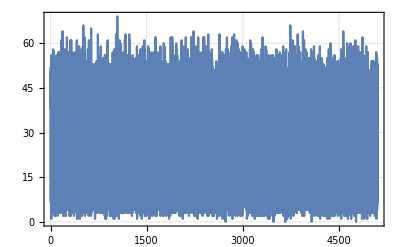
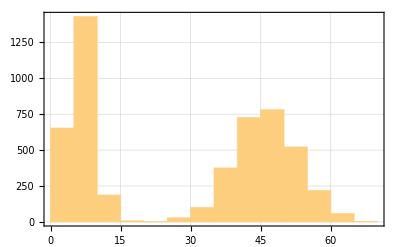
{(4.34182×10^8 | 6. | 3.01511×10^6 | 49999. | 45220. | 4.35617×10^8 | 28929. | 499999.
4.34182×10^8 | 6. | 3.01511×10^6 | 49999. | 43254. | 4.35617×10^8 | 28929. | 499999.
4.34182×10^8 | 52. | 3.01511×10^6 | 49999. | 32113. | 4.32761×10^8 | 28929. | 499999.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

```mathematica
(*dataset[[;;,5]]-=0.;
th0=GroupBy[dataset,#[[4]]&]//KeySort;*)
```

```mathematica
(*dataset=th0[[#]]&[5];*)
```

```mathematica
(*th0//Keys*)
```

```mathematica
(*get parameters*)
timeDelayUS=parameters["time_ramsey_delay_us"];
```

## Process

### Preprocess

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1./(2.^16.-1.)1.,1}];
```

```mathematica
(*(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];*)
(*(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];*)
```

```mathematica
(*(*phase unwrap & sort*)
datasetProcessed[[;;,1]]=Mod[datasetProcessed[[;;,1]],1,-0.5];
datasetProcessed=SortBy[datasetProcessed,First];*)
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=Values[CollateData[#,{1}]]&/@{dsR,dsB};
	dsRawPlot={dsR,dsR,dsB,dsB};
	(*process phonon number*)
	dsN=dsR;
	dsN[[;;,2]]=CoherentC[dsR[[;;,2]]/dsB[[;;,2]]];,

"RAP",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];,

"729",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	dsRawPlot={dsN,dsN};
];
```

## Fit

```mathematica
(*fit function*)
fitfunc=α*Cos[(periodicity*1.*π)*(ϕ-ϕ0)]^2.+δ;
(*fitConstraintsDJ={α>0.,0.5>=ϕ0>=-0.5,δ>0.};*)
fitConstraintsDJ={δ>0.,-1.<=ϕ0<=1.};
```

```mathematica
(*guess fit values*)
(*fitGuessDJ={
{α,Abs[Subtract@@MinMax[dsN[[;;,2]]]]/2.},
{ϕ0,First@dsN[[Ordering[dsN[[;;,2]],-1],1]]},
{δ,Min[dsN[[;;,2]]]}
}*)
fitGuessDJ={
{α,Abs[Subtract@@MinMax[dsN[[;;,2]]]]/2.},
{ϕ0,0.5-First@dsN[[Ordering[dsN[[;;,2]],-1],1]]},
{δ,Min[dsN[[;;,2]]]+Abs[Subtract@@MinMax[dsN[[;;,2]]]]/4.}
}
```

{{α,0.337375},{ϕ0,-0.470016},{δ,0.527182}}

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[dsN,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
ϕ
];
]
```

{0.0091824,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

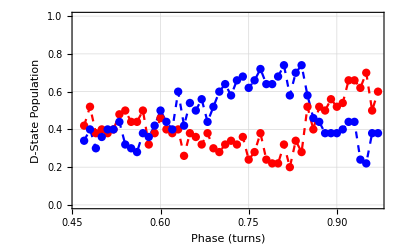

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["Phase Sweep ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]},
{Blue,PointSize[0.015]},
{Blue,Dashed,Thickness[0.004]}
},
Joined->{
False,True,
False,True
},
ImageSize->Scaled[0.45]
]
```

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,(*Automatic*)(*Full*)1.}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["Phase Sweep ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[
dataPhononPlot
,
fitPlot
],
dataProbPlot
};
```

## Show

```mathematica
1-0.939
```

0.061

| Estimate | Standard Error | Confidence Interval
α | 1.05242 | 0.151026 | {0.748766,1.35608}
ϕ0 | -0.756136 | 0.0107064 | {-0.777662,-0.734609}
δ | 0.648377 | 0.0372083 | {0.573565,0.723189}

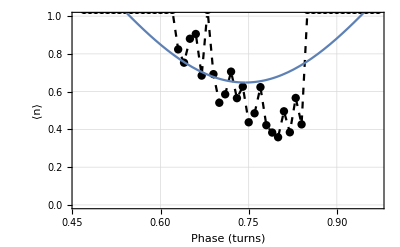
{-Graphics-,-Graphics-}

```mathematica
fitParams
summaryFigure
```

```mathematica
1-0.92942
```

0.07058

## General Ramsey Sweep

```mathematica
rid=133047;
freqReadoutCol=6;
countCol=2;
sweepCol=8;
```

```mathematica
timeFudgeUS=100.;(*adjust if bad fit: ~100 for small delay tims (~100us), ~0 for long delays (~1000us)*)
freqScale=1.*^3;
(*ϕ0=0.;(*phase offset*)*)
```

```mathematica
procStyle="SBR";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
fitStyle="COS";(*full ramsey fit: "RAM", cosine-only fit: "COS"*)
```

## Import

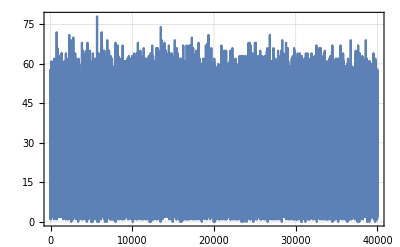
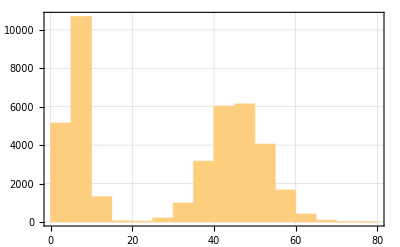
{(4.34182×10^8 | 49. | 3.01511×10^6 | 49999. | 32768. | 4.32761×10^8 | 28929. | 787573.
4.34182×10^8 | 9. | 3.01511×10^6 | 49999. | 32768. | 4.32761×10^8 | 28929. | 1.37375×10^6
4.34182×10^8 | 44. | 3.01511×10^6 | 49999. | 32768. | 4.32761×10^8 | 28929. | 401802.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

```mathematica
(*extract important parameters*)
(*timeRamseyUS=parameters["time_ramsey_delay_us"];
timeDisplaceUS=parameters["time_eggs_heating_us"];
timePulseshapeUS=parameters["time_pulse_shape_rolloff_us"]*parameters["enable_pulse_shaping"];
phaseRamseyTurns=First@parameters["phase_ramsey_anti_turns_list"];
linetrigStatus=parameters["enable_linetrigger"];
(*calculate approximate displacement time*)
timeEGGSus=timeDisplaceUS+timePulseshapeUS*(2.*0.5);*)

(*For squeezing code*)
timeRamseyUS=parameters["time_ramsey_delay_us"];
timeDisplaceUS=parameters["time_squeeze_us_list"];
timePulseshapeUS=0;
phaseRamseyTurns=First@parameters["phase_antisqueeze_turns_list"];
linetrigStatus=0;
(*calculate approximate displacement time*)
timeEGGSus=timeDisplaceUS+timePulseshapeUS*(2.*0.5);
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,4295ftwToFrequencyMHz,1}];
```

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=Values[CollateData[#,{1}]]&/@{dsR,dsB};
	dsRawPlot={dsR,dsB};
	(*process phonon number*)
	dsN=dsR;
	dsN[[;;,2]]=CoherentC[dsR[[;;,2]]/dsB[[;;,2]]];,

"RAP",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{2}]];
	dsRawPlot={dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];,

"729",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	dsRawPlot={dsN};
];
```

## Fit

### Prepare Ramsey Fit

```mathematica
(*set parameters*)
(*timeHeatUS=parameters["time_eggs_heating_us"]*1.5;
timeDelayUS=parameters["time_ramsey_delay_us"];*)
timeHeatUS=25.;
timeDelayUS=100.;
```

```mathematica
fitfuncRAM=α*Sinc[(2.*π*freqScale)((x-β)*τ)/2.+1.*^-5]^2.*
Sin[(2.*π*freqScale)*(((x-β)*(T+τ))/2.)+(2.*π*ϕ)]^2.+
δ;
```

```mathematica
fitConstraintsRAM={α>0.,0.5>=ϕ>=-0.5,δ>0.};
```

```mathematica
fitGuessRAM={
{α,Abs[Subtract@@MinMax[dsN[[;;,2]]]]},(*amplitude*)
{β,First@dsN[[Ordering[dsN[[;;,2]],-1],1]]},(*linecenter*)
{ϕ,ϕ0},(*phase shift*)
{T,(timeDelayUS+timeFudgeUS)*1.*^-3},(*delay time*)
{τ,timeHeatUS*1.*^-3},(*pulse time*)
{δ,Min[dsN[[;;,2]]]}(*offset*)
};
```

```mathematica
(*guessPhononAmpl=ArcSin[Sqrt[guessPhononAmpl]]/(π*timeHeatUS);*)
```

```mathematica
(*(*set fixed values*)
fitfunc=fitfunc/.{
τ->(timeHeatUS),
T->(timeDelayUS),
β->Mean[dsN[[;;,1]]]
(*ϕ->0.*)
};*)
```

### Prepare Cosine Fit

```mathematica
fitfuncCOS=α*Cos[(T*1.*π)*(x-ϕ0)]^2.+δ;
```

```mathematica
fitConstraintsCOS={α>0.,0.5>=ϕ0>=-0.5,δ>0.};
```

```mathematica
fitGuessCOS={
{α,Abs[Subtract@@MinMax[dsN[[;;,2]]]]},
{ϕ0,First@dsN[[Ordering[dsN[[;;,2]],-1],1]]},
{T,(timeRamseyUS+timeFudgeUS)*1.*^-3},
{δ,Min[dsN[[;;,2]]]}
};
```

### Do Fit!

```mathematica
(*select target fit styles*)
Switch[fitStyle,

"COS",
	fitfuncDJ=fitfuncCOS;
	fitConstraintsDJ=fitConstraintsCOS;
	fitGuessDJ=fitGuessCOS;,

"RAM",
	fitfuncDJ=fitfuncRAM;
	fitConstraintsDJ=fitConstraintsRAM;
	fitGuessDJ=fitGuessRAM;
]
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[dsN,
Join[{fitfuncDJ},fitConstraintsDJ],
fitGuessDJ,
x
];
]
```

NonlinearModelFit::srect: Value 0.001 (100.+Missing[KeyAbsent,time_ramsey_delay_us]) in search specification {T,0.001 (100.+Missing[KeyAbsent,time_ramsey_delay_us])} is not a number or array of numbers.

{0.0014626,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

NonlinearModelFit::srect: Value 0.001 (100.+Missing[KeyAbsent,time_ramsey_delay_us]) in search specification {T,0.001 (100.+Missing[KeyAbsent,time_ramsey_delay_us])} is not a number or array of numbers.

```mathematica
fitfuncDJ
```

δ+α Cos[3.14159 T (x-ϕ0)]^2.

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,dsN[[1,1]],dsN[[-1,1]]}
];
```

NonlinearModelFit::srect: Value 0.001 (100.+Missing[KeyAbsent,time_ramsey_delay_us]) in search specification {T,0.001 (100.+Missing[KeyAbsent,time_ramsey_delay_us])} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
dsN,
dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,Full}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
(*Style["Frequency (Hz)",{Black,Directive[15]}],*)
Style["Time (us)",{Black,Directive[15]}],
Style["Ramsey ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True},
ImageSize->Scaled[0.45]
],
fitPlot
],
ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.0}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
(*Style["Frequency (Hz)",{Black,Directive[15]}],*)
Style["Time (us)",{Black,Directive[15]}],
Style["Ramsey ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black},
ImageSize->Scaled[0.45]
]
};
```

## Show

{0,KeyAbsent}

ParameterConfidenceIntervalTable

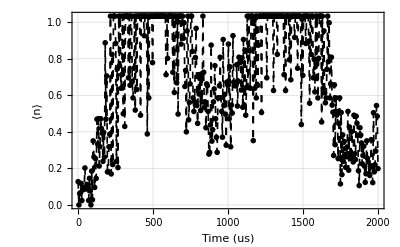
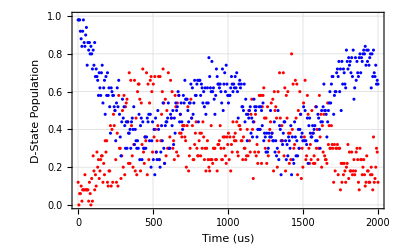

```mathematica
{linetrigStatus,phaseRamseyTurns}
fitParams
summaryFigure
```

```mathematica
RandomSample[{100,200,500,888,1000,1500,2000,2500,3000,3500,4000(*,4500,5000,6000,7000,8000*)}];
```

```mathematica
(*(1.*^3)*{0.0025,6.*^-5}*1000./#&[3000]*)
```

## General Heating Rate

```mathematica
(*general config*)
rid=132854;
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
countCol=2;(*raw count column*)
sweepCol=7;(*sweep column*)
```

```mathematica
(*sweep formatting*)
sweepColConversion=1.;100./(2^14-1);1.*ns/ms;(*convert sweep column to target units*)
sweepColLabel="Displacement (α)";(*x-axis label for sweep*)
```

```mathematica
(*specific config*)
procStyle="RAP";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
```

## Import

```mathematica
(*todo: get relevant params*)
```

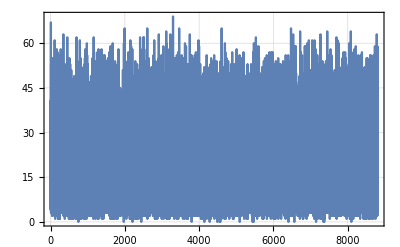
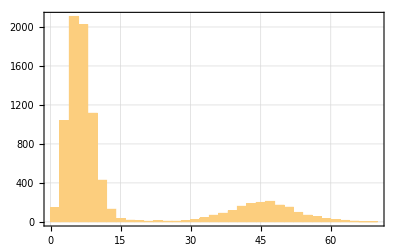
{(-1. | 41. | 8.6×10^7 | 0. | 0. | 0. | 0.103448 | 0. | 256.
-1. | 6. | 8.6×10^7 | 0. | 0. | 0. | 0.390805 | 0. | 256.
-1. | 5. | 8.6×10^7 | 0. | 0. | 0. | 0.183908 | 0. | 256.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]*)
};
```

```mathematica
(*get parameters*)
(*timeDelayUS=parameters["time_ramsey_delay_us"];*)
```

## Process

### Preprocess

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,sweepColConversion,1}];
```

```mathematica
(*tmp remove*)
datasetProcessed[[;;,2]]=5.2/2.*(datasetProcessed[[;;,2]])^1.;
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=Values[CollateData[#,{1}]]&/@{dsR,dsB};
	dsRawPlot={dsR,dsB};
	(*process phonon number*)
	dsN=dsR;
	dsN[[;;,2]]=CoherentC[dsR[[;;,2]]/dsB[[;;,2]]];,

"RAP",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	dsRawPlot={dsN};
	(*dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];,*)
	dsN[[;;,2]]=dsN[[;;,2]]/(1.-dsN[[;;,2]]);,

"729",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	dsRawPlot={dsN};
];
```

## Fit

```mathematica
(*fit linear model!*)
AbsoluteTiming[
fitRes=LinearModelFit[
dsN,
{1,x},
x
];
]
```

{0.0004191,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Raw Probability

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
{
First@dsRawPlot,First@dsRawPlot
},
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style[sweepColLabel,{Black,Directive[15]}],
Style[StringForm["Heating Rate (``) - RID: ``",procStyle,rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Phonon Number

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[x],
{x,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,(*Automatic*)(*Full*)1.}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style[sweepColLabel,{Black,Directive[15]}],
Style[StringForm["Heating Rate (``) - RID: ``",procStyle,rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Summary

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[
{
dataPhononPlot,
fitPlot
},
PlotRange->{
{Full,Full},
{Full,Full}
},
PlotLegends->{"aa","bb"}
],
dataProbPlot
};
```

## Show

| Estimate | Standard Error | Confidence Interval
1 | 3.84174 | 1.3474 | {1.16319,6.52028}
x | 2.63142 | 0.895035 | {0.852155,4.41069}

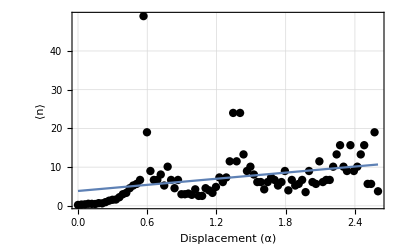
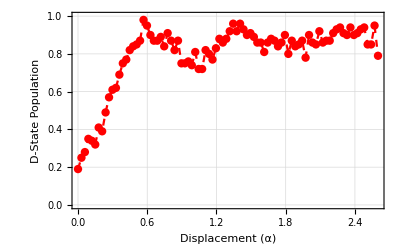

```mathematica
fitParams
summaryFigure
```

## Free Induction Decay

```mathematica
(*general config*)
rid=132996;
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
countCol=2;(*raw count column*)
sweepCol=3;(*sweep column*)
```

```mathematica
(*specific config*)
procStyle="729";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
periodicity=1.;(*number of oscillations*)
ωGuess=40.;(*guess detuning (in x2π kHz)*)
```

## Import

```mathematica
(*todo: get relevant params*)
```

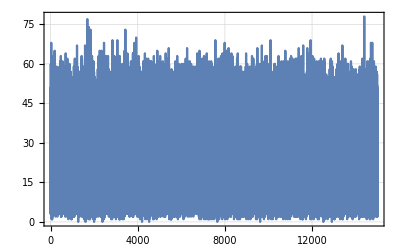
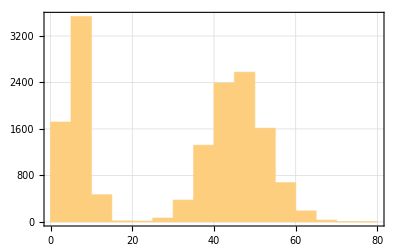
{(4.34137×10^8 | 37. | 1.90268×10^6 | 16384. | 1.6×10^7
4.34137×10^8 | 6. | 1.84899×10^6 | 16384. | 1.6×10^7
4.34137×10^8 | 51. | 1.58054×10^6 | 16384. | 1.6×10^7),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]*)
};
```

```mathematica
(*get parameters*)
(*timeDelayUS=parameters["time_ramsey_delay_us"];*)
```

## Process

### Preprocess

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,μs,1}];
```

### Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=Values[CollateData[#,{1}]]&/@{dsR,dsB};
	dsRawPlot={dsR,dsB};
	(*process phonon number*)
	dsN=dsR;
	dsN[[;;,2]]=CoherentC[dsR[[;;,2]]/dsB[[;;,2]]];,
	
	(**)


"RAP",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	dsRawPlot={dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];,

"729",
	dsN=Values[CollateData[datasetProcessed[[;;,{2,3}]],{1}]];
	(*dsN[[;;,2]]=dsN[[;;,2]]/(1.-dsN[[;;,2]]);*)
	dsRawPlot={dsN};
];
```

## Fit

```mathematica
(*prepare fitting*)
fitfunc=(A*Exp[-(t/τ)^1.])/2.*Cos[(ω*1.*π)*(t-t0)]+COff;
fitConstraints={
(*{α>0.,0.5>=ϕ0>=-0.5,δ>0.};*)
A>0.,
COff>0.,
τ>0.
};
```

```mathematica
fitGuess={
{A,Abs[Subtract@@MinMax[dsN[[;;,2]]]]},
{ω,ωGuess},
{τ,1.},
{t0,0.},
{COff,Abs[Subtract@@MinMax[dsN[[;;,2]]]]/2.}
}
```

{{A,0.56},{ω,40.},{τ,1.},{t0,0.},{COff,0.28}}

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
Join[{fitfunc},fitConstraints],
fitGuess,
t
];
]
```

{0.0196487,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Fitted Results

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[x],
{x,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Thickness[0.007],Opacity[0.8]}
];
```

### Raw Results

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
{
First@dsRawPlot,First@dsRawPlot
},
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Time (ms)",{Black,Directive[15]}],
Style["Free Induction Decay ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Converted Results

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,(*Automatic*)Full}
},
FrameLabel->{ 
{Style["D-State Probability (P_D)",{Black,Directive[15]}],None},
{
Style["Time (ms)",{Black,Directive[15]}],
Style["Free Induction Decay ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

### Summary Figure

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[
dataPhononPlot
,
fitPlot
],
dataProbPlot
};
```

## Show

| Estimate | Standard Error | Confidence Interval
A | 2.357 | 0.840607 | {0.695574,4.01843}
ω | 37.0657 | 0.0690064 | {36.9293,37.2021}
τ | 0.942494 | 0.18506 | {0.57673,1.30826}
t0 | -0.136766 | 0.0034413 | {-0.143568,-0.129964}
COff | 0.387544 | 0.0040029 | {0.379633,0.395456}

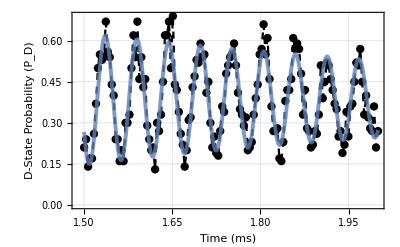
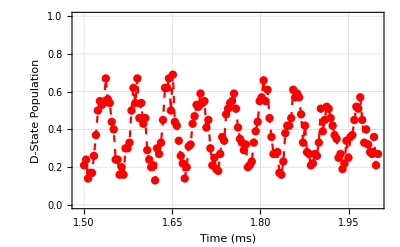

```mathematica
fitParams
summaryFigure
```

```mathematica
3000/71.
```

42.2535

```mathematica
A
```

A

## General Freq Sweep - Development

```mathematica
rid=96585;
ϕ0=0.;
phaseCol=1;
holdoffCol=5;
```

```mathematica
holdoffIdx=1;
```

## Import

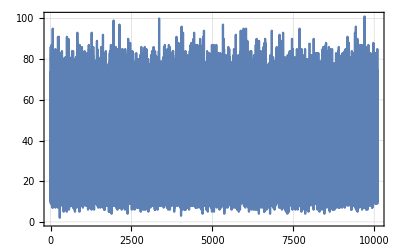
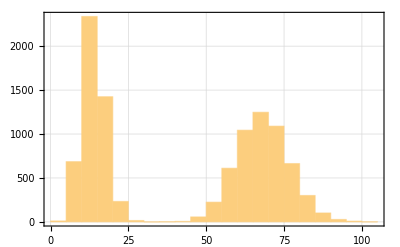
{(4.35228×10^8 | 13. | 2.×10^6 | 0. | 99999.
4.35229×10^8 | 10. | 2.×10^6 | 0. | 99999.
4.35227×10^8 | 70. | 2.×10^6 | 0. | 99999.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*extract important parameters*)
timeRamseyUS=First@parameters["time_delay_us_list"];
timePulseUS=parameters["time_pulse_us"];
phaseRamseyTurns=First@parameters["phase_ramsey_turns_list"];
holdoffTimesMU=(dataset[[;;,holdoffCol]]//DeleteDuplicates//Sort);
```

## Process

```mathematica
(*extract only points for a given holdoff time*)
dataset=Select[dataset,#[[holdoffCol]]==holdoffTimesMU[[holdoffIdx]]&];
```

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{phaseCol,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.}];
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

## Fit

### Complete Ramsey Fit

```mathematica
(*(*displace ramsey fit function*)
fitfunc=4. Ω^2. τ^2. Sinc[(2.*π)*((x-β)*τ)/2.+1.*^-5]^2. Sin[(2.*π)*(((x-β)*(T+τ))/2.+ϕ)]^2.+δ;
(*set fixed values*)
fitfunc=fitfunc/.{
τ->(timePulseUS(**1.*^-6*)),
T->(timeRamseyUS(**1.*^-6*)),
β->Mean[datasetProcessed[[;;,1]]]
(*ϕ->0.*)
};*)
```

```mathematica
(*(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc
},
{
{Ω,1.*^4},
{β,Mean[datasetProcessed[[;;,1]]]},
{τ,timePulseUS(**1.*^-6*)},
{T,timeRamseyUS(**1.*^-6*)},
{δ,Mean[datasetProcessed[[;;,2]]]},
{ϕ,0.}
},
x
];
]*)
```

### General Sine Fit

```mathematica
(*general sine fit*)
fitfunc=α*Cos[(2.*π)*(T)*(x-β)+ϕ]^2.+δ;

(*set fixed values*)
fitfunc=fitfunc/.{
T->(timeRamseyUS+timePulseUS)(**1.*^-6*),
ϕ->(2.*π)*phaseRamseyTurns
}
```

δ+α Cos[0.+12585.2 (x-β)]^2.

```mathematica
(*guess initial values*)
guessα=1.0*(Max[datasetProcessed[[;;,2]]]-Min[datasetProcessed[[;;,2]]]);
guessβ=Mean[datasetProcessed[[;;,1]]];
guessT=(timeRamseyUS+timePulseUS)(**1.*^-6*);
guessδ=Mean[datasetProcessed[[;;,2]]];
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
datasetProcessed,
{
fitfunc
},
Transpose[{
{α,β,T,δ},
{guessα,guessβ,guessT,guessδ}
}],
x
];
]
```

{0.0054475,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,datasetProcessed[[1,1]],datasetProcessed[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
datasetProcessed,
datasetProcessed
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["P_(S - 1/2)",{Black,Directive[15]}],None},
{
Style["Frequency (MHz)",{Black,Directive[15]}],
Style["729nm Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

## Show

(101.335065
0.
0.099999)

| Estimate | Standard Error | Confidence Interval
α | 0.301834 | 0.0118409 | {0.278333,0.325334}
β | 101.335 | 1.55513×10^-6 | {101.335,101.335}
T | 2003. | 0. | {2003.,2003.}
δ | 0.314237 | 0.00728254 | {0.299784,0.328691}

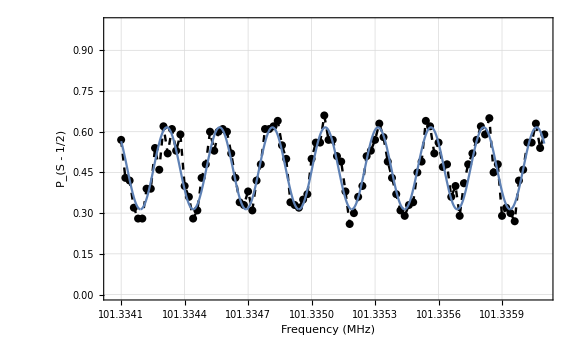

```mathematica
{NumberForm[fitParams[[1,1,3,2]],9],
phaseRamseyTurns,
holdoffTimesMU[[holdoffIdx]]/1.*^6}//MatrixForm
fitParams
summaryFigure
```

```mathematica
{0.0015,3.*^-5}*(1000.)*1000./3000.
```

{0.5,0.01}

```mathematica
Join[{timeRamseyUS},fitParams[[1,1,2,2;;]]]
```

{2000.,-0.268363,0.0135732,{-0.295302,-0.241424}}

## SDR X2 freq sweep

```mathematica
rid=115466;
ϕ0=0.;
```

```mathematica
freqReadoutCol=1;
countCol=2;
freqSweepCol=4;
phaseSweepCol=5;
```

## Import

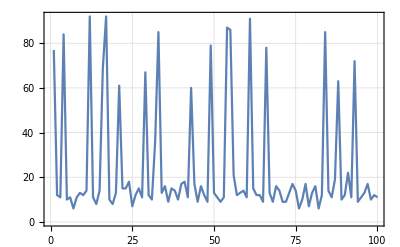
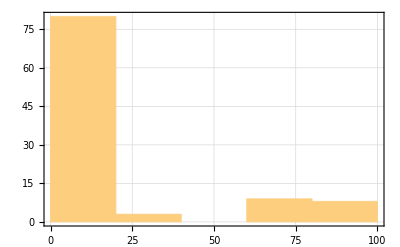
{(4.35632×10^8 | 77. | 8.6×10^7 | 150. | 0. | 0.897 | 24279.
4.35632×10^8 | 16. | 8.6×10^7 | 141.667 | 0. | 0.897 | 24279.
4.35632×10^8 | 14. | 8.6×10^7 | 125. | 0. | 0.897 | 24279.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;;;50]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#[[;;;;50]],ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*ds0=dataset;
(*dataset[[;;,5]]-=0;*)
th0=GroupBy[dataset,#[[5]]&]//KeySort;*)
```

```mathematica
(*dataset=th0[[#]]&[6];*)
```

```mathematica
(*th0[[6;;]]//Keys*)
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{freqReadoutCol,freqSweepCol,phaseSweepCol,countCol}]],4];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{ftwToFrequencyMHz,1.*^-0,1.*^-0,1}
];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,4}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,4}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

```mathematica
(*tmp fix*)
dsN[[;;,1]]+=1.*^-7;
```

## Fit

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
A*x^k+B
},
{
{A,1.4},
{k,2.5},
{B,0.}
},
x
];
]
```

{0.0020035,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
dsN,
dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,Full}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["SuperRes - X2 Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True},
ImageSize->Scaled[0.45]
],
fitPlot
],
ListPlot[
{
dsR,
dsB
},
PlotRange->{
{Automatic,Automatic},
{0.,1.0}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["SuperRes - X2 Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black},
ImageSize->Scaled[0.45]
]
};
```

## Show

| Estimate | Standard Error | Confidence Interval
A | 6.99523×10^-9 | 2.54193×10^-8 | {-4.57212×10^-8,5.97116×10^-8}
k | 3.30298 | 0.691364 | {1.86918,4.73678}
B | 0.0907403 | 0.0125256 | {0.0647639,0.116717}

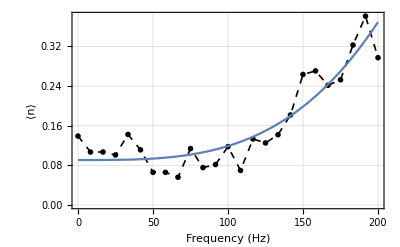
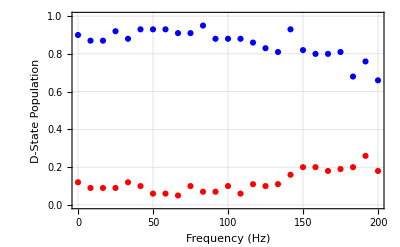

```mathematica
fitParams
summaryFigure
```

## batch in small groups

```mathematica
(*group dataset for each freq*)
batchData=GroupBy[datasetProcessed,#[[2]]&]//KeySort;
```

### Group In Small Batches

```mathematica
(*process data in fixed batches - separately process freq/phase*)
KKFunc[data_,batchSize_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
sc1,scR,scB,scR2,scB2
},

sc1=GroupBy[data,#[[1]]<freqDiff&];
scR=sc1[True];
scB=sc1[False];

scR2=(Mean/@ArrayReshape[
scR[[;;IntegerPart[Length[scR]/batchSize]*batchSize]],
{IntegerPart[Length[scR]/batchSize],batchSize,Dimensions[scR][[2]]}
])[[;;,4]];
scB2=(Mean/@ArrayReshape[
scB[[;;IntegerPart[Length[scB]/batchSize]*batchSize]],
{IntegerPart[Length[scB]/batchSize],batchSize,Dimensions[scB][[2]]}
])[[;;,4]];
Return[Mean@(CoherentC[scR2/(scB2+1.*^-7)])];
];
```

```mathematica
(*dsBatch2N=Transpose[
{
Keys[batchData],
KKFunc[#,2]&/@Values[batchData]
}
];*)
```

```mathematica
(*dsBatch5N=Transpose[
{
Keys[batchData],
KKFunc[#,5]&/@Values[batchData]
}
];*)
```

```mathematica
(*dsBatch10N=Transpose[
{
Keys[batchData],
KKFunc[#,10]&/@Values[batchData]
}
];*)
```

### Group By Phase

```mathematica
(*process data in fixed batches - separately process freq/phase*)
KKFuncPhase[data_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
sc1,scR,scB,scR2,scB2
},

sc1=GroupBy[data,#[[1]]<freqDiff&];
scR=sc1[True];
scB=sc1[False];

scR2=(Mean/@(GroupBy[scR,#[[3]]&]//KeySort//Values))[[;;,4]];
scB2=(Mean/@(GroupBy[scB ,#[[3]]&]//KeySort//Values))[[;;,4]];
Return[Mean@(CoherentC[scR2/(scB2+1.*^-7)])];
];
```

```mathematica
dsPhaseN=Transpose[
{
Keys[batchData],
KKFuncPhase[#]&/@Values[batchData]
}
];
```

### Single-Point Measurement - RSB Only

```mathematica
freqDiff=Mean[datasetProcessed[[;;,1]]];
dsSPRSB=Select[datasetProcessed,#[[1]]<freqDiff&];
dsSPRSB=GroupBy[dsSPRSB,#[[2]]&]//KeySort;
```

```mathematica
(*process data in fixed batches - separately process freq/phase*)
KKFuncSPRSB[data_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
scR,scR2
},
scR=Select[data,#[[1]]<freqDiff&][[;;,4]];
Return[CoherentR[Mean@scR]];
];
```

```mathematica
dsSPRSBN=Transpose[
{
Keys[batchData],
KKFuncSPRSB[#]&/@Values[batchData]
}
];
```

## tmp remove 2

```mathematica
(*dsMeanIdealN=dsN;
dsMeanIdealN[[;;,2]]/=2.;*)
```

```mathematica
(*dsMinN=dsN;
dsMinR=dsR;
dsMinB=dsB;*)
```

```mathematica
(*dsMeanN=dsMaxN;
dsMeanN[[;;,2]]/=2.;*)
```

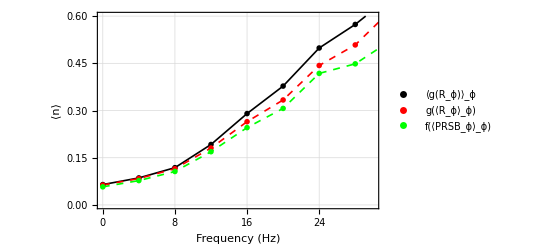

```mathematica
ListPlot[
{
dsPhaseN,dsPhaseN,
dsAllN,dsAllN,
dsSPRSBN,dsSPRSBN
},
PlotRange->{
{Automatic,30.},{0.,0.6}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Estimator Comparison\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotLegends->{
"⟨g(R_ϕ)⟩_ϕ",None,
"g(⟨R_ϕ⟩_ϕ)",None,
"f(⟨PRSB_ϕ⟩_ϕ)",None
},
PlotStyle->{
{Black,PointSize[0.01]},{Black,Thickness[0.003]},
{Red,PointSize[0.01]},{Red,Dashed,Thickness[0.003]},
{Green,PointSize[0.01]},{Green,Dashed,Thickness[0.003]},
{Blue,PointSize[0.01]},{Blue,Dashed,Thickness[0.003]}
},
Joined->{
False,True,
False,True,
False,True,
False,True
},
ImageSize->Scaled[0.45]
]
```

## SDR Estimator comparison tmp

## tmp remove

```mathematica
(*(*readout freq, x2 freq, phase*)
datasetProcessedTMP=ThresholdCounts[dataset[[;;,{1,4,5,countCol}]],4];
batchData=GroupBy[datasetProcessedTMP,#[[2]]&]//KeySort;*)
```

```mathematica
(*KKFunc[data_,batchSize_]:=Module[
{
freqDiff=Mean[data[[;;,1]]],
sc1,scR,scB,scR2,scB2
},

sc1=GroupBy[data,#[[1]]<freqDiff&];
scR=sc1[True];
scB=sc1[False];

scR2=(Mean/@ArrayReshape[
scR[[;;IntegerPart[Length[scR]/batchSize]*batchSize]],
{IntegerPart[Length[scR]/batchSize],batchSize,Dimensions[scR][[2]]}
])[[;;,4]];
scB2=(Mean/@ArrayReshape[
scB[[;;IntegerPart[Length[scB]/batchSize]*batchSize]],
{IntegerPart[Length[scB]/batchSize],batchSize,Dimensions[scB][[2]]}
])[[;;,4]];
Return[Mean@(CoherentC[scR2/(scB2+1.*^-7)])];
];*)
```

```mathematica
dsBatch2N=Transpose[
{
Keys[batchData],
KKFunc[#,2]&/@Values[batchData]
}
];
```

```mathematica
(*dsBatch5N=Transpose[
{
Keys[batchData],
KKFunc[#,5]&/@Values[batchData]
}
];*)
```

```mathematica
(*dsBatch10N=Transpose[
{
Keys[batchData],
KKFunc[#,10]&/@Values[batchData]
}
];*)
```

## tmp remove 2

```mathematica
(*dsMeanIdealN=dsN;
dsMeanIdealN[[;;,2]]/=2.;*)
```

```mathematica
(*dsMinN=dsN;
dsMinR=dsR;
dsMinB=dsB;*)
```

```mathematica
(*dsMaxN=dsN;
dsMaxR=dsR;
dsMaxB=dsB;*)
```

```mathematica
(*dsAllN=dsN;
dsAllR=dsR;
dsAllB=dsB;*)
```

```mathematica
(*dsMeanN=dsMaxN;
dsMeanN[[;;,2]]/=2.;*)
```

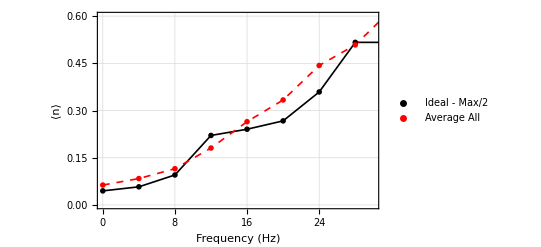

```mathematica
ListPlot[
{
(*dsMeanIdealN,dsMeanIdealN,*)
dsMeanN,dsMeanN,
dsAllN,dsAllN
(*dsBatch2N,dsBatch2N,
dsBatch5N,dsBatch5N*)
(*dsBatch10N,dsBatch10N*)
},
PlotRange->{
{Automatic,30.},
{0.,0.6}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Estimator Comparison\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotLegends->{
"Ideal - Max/2",None,
"Average All",None,
"Batched - 2 Points",None,
"Batched - 5 Points",None
},
PlotStyle->{
{Black,PointSize[0.01]},{Black,Thickness[0.003]},
{Red,PointSize[0.01]},{Red,Dashed,Thickness[0.003]},
{Green,PointSize[0.01]},{Green,Dashed,Thickness[0.003]},
{Blue,PointSize[0.01]},{Blue,Dashed,Thickness[0.003]}
},
Joined->{
False,True,
False,True,
False,True,
False,True
},
ImageSize->Scaled[0.45]
]
```

# Bichromatic (wigner) phase sweep wrt QVSA

```mathematica
RandomSample[Range[0,1000,100]]
```

{600,800,900,200,300,400,0,100,1000,500,700}

```mathematica
rid=117186;
countCol=2;
phaseCol=4;
```

```mathematica
βCalib=3.653/50.;αCalib=20./500.;
guessαβ0=0.1*(βCalib)*(αCalib);
guessϕ=-0.25;
```

```mathematica
guessConstraints={
(*-1.<=A<1.,
-10.<=αβ<=10.*)
(*αβ==7.0,*)
(*1.<=A<=0.*)
(*-0.3<=δ<=0.,
-1.<=A<=-0.05*)
};
```

```mathematica
3.61157
```

3.61157

## TMP hide

## Import

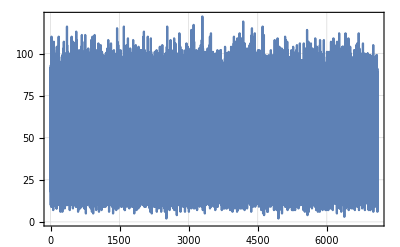
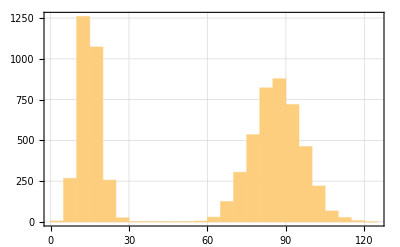
{(0. | 92. | 19999. | 16852.
0. | 82. | 19999. | 34640.
0. | 18. | 19999. | 9362.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*extract important parameters*)
timeQVSAUS=parameters["time_superresolution_stop_us"];
timeFullUS=parameters["time_eggs_heating_us"];
timeBichromaticUS=parameters["time_char_phase_sweep_us"];
(*todo: get PSK and num*)
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{phaseCol,countCol}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{1./(2^16-1.),1.}];
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

```mathematica
(*phase unwrap & sort*)
datasetProcessed[[;;,1]]=Mod[datasetProcessed[[;;,1]],1,-0.5];
datasetProcessed=SortBy[datasetProcessed,First];
```

## Fit

```mathematica
(*use dataset parameters to inform guess values*)
timeAdjustUS=timeQVSAUS-2.*UnitStep[(timeQVSAUS-1.)-timeFullUS/2]*Mod[timeQVSAUS,timeFullUS/2,0];(*adjusted time accounting for PSK*)
guessαβ=guessαβ0*timeAdjustUS*timeBichromaticUS
```

5.8448

### Coherent Fringes Fit

```mathematica
(*general sine fit*)
fitfunc=0.5*(1.+A*Cos[2.*αβ*Sin[(2.*π)*(θ-ϕ)]])+δ;
(*fitfunc=A*Cos[αβ*Sin[(2.*π)*(θ-ϕ)]]^2.+δ;*)
```

```mathematica
(*guess initial values*)
guessA=-1.*(Max[datasetProcessed[[;;,2]]]-Min[datasetProcessed[[;;,2]]])
guessδ=Mean[datasetProcessed[[;;,2]]]-0.5
```

-0.8

-0.0907143

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
datasetProcessed,
Join[{fitfunc},guessConstraints],
Transpose[{
{A,αβ,ϕ,δ},
{guessA,guessαβ,guessϕ,guessδ}
}],
θ,
MaxIterations->1*^6
];
]
```

{0.0008891,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,datasetProcessed[[1,1]],datasetProcessed[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
datasetProcessed,
datasetProcessed
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["P_(D - 5/2)",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["QVSA vs Cat Phase (T_QVSA = "<>ToString[timeQVSAUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

## Show

```mathematica
guessαβ
```

5.8448

| Estimate | Standard Error | Confidence Interval
A | -0.65106 | 0.0138885 | {-0.678789,-0.62333}
αβ | 6.594 | 0.0181487 | {6.55776,6.63023}
ϕ | -0.267813 | 0.000369878 | {-0.268551,-0.267074}
δ | -0.0202843 | 0.00522282 | {-0.030712,-0.00985662}

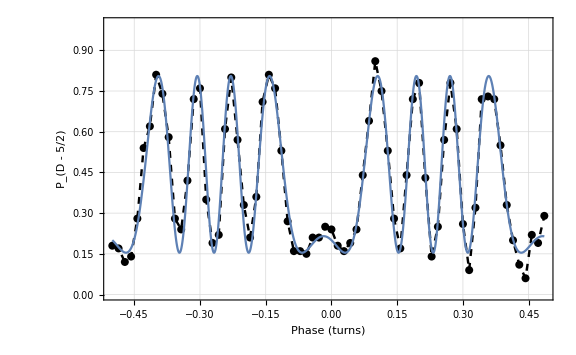

```mathematica
fitParams
summaryFigure
```

```mathematica
0.25-0.223305
```

0.026695

```mathematica
0.02828*360
```

10.1808

```mathematica
ArcTan[0.607337/4.03156]/(π/180.)
```

8.56694

```mathematica
ArcTan[1]/(π/180.)
```

45.

## plot summary

## Create Dataset

```mathematica
dsDJ={
{100,{-0.047234,0.00608},{0.974542,0.0363463}},
{200,{-0.00085,0.00299},{1.61851,0.0705}},
{300,{0.01165,0.0048931},{2.21492,0.0677491}},
{400,{-0.00811,0.001927},{2.7552,0.03894}},
{500,{-0.0066,0.001296},{3.7311,0.0313}},
{600,{0.00179,0.0017983},{3.11122,0.0515598}},
{700,{-0.003517,0.00297},{2.2909,0.0392868}},
{800,{0.000599644,0.00225},{1.71381,0.00297}},
{900,{0.028922,0.0056951},{0.833862,0.426588}}
(*{1000,{-0.0283,0.0033},{2.35274,0.0324992}}*)
};
(*mod phase values to [-0.5,0.5] (i.e. [-π,π])*)
(*dsDJ[[;;,2,1]]=Mod[dsDJ[[;;,2,1]],0.5,-0.25];
dsDJ[[8;;,2,1]]=Mod[dsDJ[[8;;,2,1]],0.5,0.];
dsDJ[[10;;,2,1]]=Mod[dsDJ[[10;;,2,1]],0.5,0.25];*)
(*dsDJ[[;;,2,1]]=Mod[dsDJ[[;;,2,1]],0.5,0.25];
dsDJ[[8;;,2,1]]=Mod[dsDJ[[8;;,2,1]],0.5,0.5];*)
(*dsDJ[[10;;,2,1]]=Mod[dsDJ[[10;;,2,1]],0.5,0.25];*)

(*create sub-datasets*)
dsϕ=Transpose[{dsDJ[[;;,1]],dsDJ[[;;,2,1]]}];
dsαβ=Transpose[{dsDJ[[;;,1]],dsDJ[[;;,3,1]]}];
```

## Create & Show Plots

{0.0005048,Null}

| Estimate | Standard Error | Confidence Interval
1 | 3.16374 | 1.03188 | {0.723733,5.60376}
t | -0.000578912 | 0.00186605 | {-0.00499142,0.0038336}

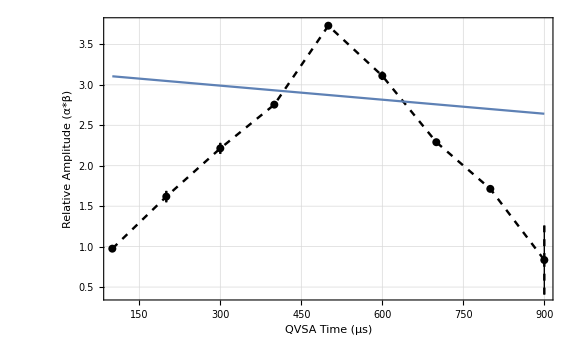

```mathematica
(*fit linear trend & plot*)
AbsoluteTiming[
ϕAmplFit=LinearModelFit[
dsαβ,
{1,t},
t,
Weights->(dsDJ[[;;,2,2]]/2)^-2
];
]
(*get fit params*)
ϕAmplParams=Style[
ϕAmplFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]
Show[
ListPlot[
{#,#},
PlotRange->{{Full,Full},{Full,Full}},
FrameLabel->{ 
{Style["Relative Amplitude (α*β)",{Black,Directive[15]}],None},
{
Style["QVSA Time (μs)",{Black,Directive[15]}],
Style["Fitted Product Amplitude",{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
Plot[
ϕAmplFit[t],
{t,dsαβ[[1,1]],dsαβ[[-1,1]]}
],
PlotRange->{{Full,Full},{Full,Full}}
(*]&[Transpose[{dsDJ[[;;,1]],dsDJ[[;;,3,1]]}]]*)
]&[Transpose[{dsDJ[[;;,1]],Around@@@dsDJ[[;;,3]]}]]
```

{0.0006928,Null}

| Estimate | Standard Error | Confidence Interval
1 | -0.0318383 | 0.00948619 | {-0.0542696,-0.00940701}
ϕ | 0.0000406591 | 0.000011989 | {0.0000123098,0.0000690085}

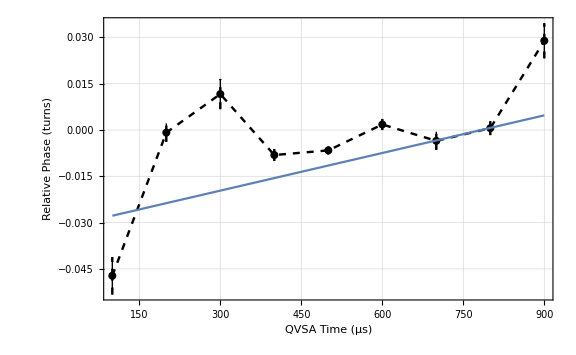

```mathematica
(*fit linear trend & plot*)
AbsoluteTiming[
ϕDriftFit=LinearModelFit[
dsϕ,
{1,ϕ},
ϕ,
Weights->(dsDJ[[;;,3,2]]/2)^-2
];]
(*get fit params*)
ϕDriftParams=Style[
ϕDriftFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]
Show[
ListPlot[
{#,#},
PlotRange->{{Full,Full},{Full,Full}},
FrameLabel->{ 
{Style["Relative Phase (turns)",{Black,Directive[15]}],None},
{
Style["QVSA Time (μs)",{Black,Directive[15]}],
Style["QVSA vs Cat Phase",{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
Plot[
ϕDriftFit[ϕ],
{ϕ,dsϕ[[1,1]],dsϕ[[-1,1]]}
],
PlotRange->{{Full,Full},{Full,Full}}
(*]&[Transpose[{dsDJ[[;;,1]],dsDJ[[;;,2,1]]}]]*)
]&[Transpose[{dsDJ[[;;,1]],Around@@@dsDJ[[;;,2]]}]]
```

# Others again